Mark Hilliker
CSE 477 G. Farin
HW2 , due 10/9 , midnight

### Turn in via Blackboard Name your file lastname_firstname_HW2.nb

Using several cubic Bezier curves, design two characters, for instance your two initials. These can be Western, Chinese, Sanskrit, Arabic, etc., fonts.
The characters need to have a thickness, or in other words, an inside. See the class log for a link to some examples from a previous semester. Be creative!

Plot the Bezier polygons and curves. Use different colors and line thickness.

Use a shear matrix to make italic versions of your characters.

Extra credit: extrude in z and thus create 3D block fonts. For this, sample each Bezier curve at 20 points
and form rectangles from corresponding points.

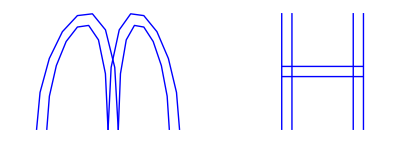

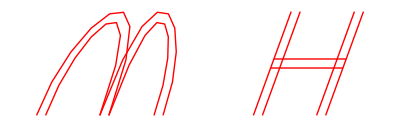

```mathematica
(* First arch of M *)
dx = 4;
thx = 0.5; (* Thickness in x *)
thy = 0.1;
mOffset = 0.5;
h1 = 10;
h2 = 5;
P1 = {{0,0},{0,h2},{dx,h1},{dx,0}};
P1b = {{0+thx,0},{0+thx,h2*(1-thy)},{dx-thx,h1*(1-thy)},{dx-thx,0}};
n1 = Length[P1]-1;
startcurve1 = Graphics[{Blue,Thick,BezierCurve[P1,SplineDegree-> n1]}];
startcurve1b = Graphics[{Blue,Thick,BezierCurve[P1b,SplineDegree-> n1]}];

(* Second arch of M *)
dx = dx - mOffset;
P2 = {{dx,0},{dx,h1},{2*dx,h2},{2*dx,0}};
P2b = {{dx+thx,0},{dx+thx,h1*(1-thy)},{2*dx-thx,h2*(1-thy)},{2*dx-thx,0}};
n2 = Length[P2]-1;
startcurve2 = Graphics[{Blue,Thick,BezierCurve[P2,SplineDegree-> n2]}];
startcurve2b= Graphics[{Blue,Thick,BezierCurve[P2b,SplineDegree-> n2]}];
dx = dx + mOffset;


(* Left vertical bar of H *)
hPrime=(h1*.65+h2)/2; (* Weighted to approximate height of M *)
P3={{3*dx,0},{3*dx,hPrime}};
P3b={{3*dx+thx,0},{3*dx+thx,hPrime}};
n3=Length[P3]-1;
lBar=Graphics[{Blue,Thick,BezierCurve[P3,SplineDegree-> n3]}];
lBarb=Graphics[{Blue,Thick,BezierCurve[P3b,SplineDegree-> n3]}];

(* Horizontal bar of H *)
P4={{3*dx,hPrime/2-thx/2},{4*dx,hPrime/2-thx/2}};
P4b={{3*dx,hPrime/2+thx/2},{4*dx,hPrime/2+thx/2}};
n4=Length[P4]-1;
hBar=Graphics[{Blue,Thick,BezierCurve[P4,SplineDegree-> n4]}];
hBarb=Graphics[{Blue,Thick,BezierCurve[P4b,SplineDegree-> n4]}];

(* Right vertical bar of H *)
P5={{4*dx,0},{4*dx,hPrime}};
P5b={{4*dx-thx,0},{4*dx-thx,hPrime}};
n5=Length[P5]-1;
rBar=Graphics[{Blue,Thick,BezierCurve[P5,SplineDegree-> n5]}];
rBarb=Graphics[{Blue,Thick,BezierCurve[P5b,SplineDegree-> n5]}];


(* Display all curves *)
curves = {startcurve1,startcurve1b,startcurve2,startcurve2b,lBar,lBarb,hBar,hBarb,rBar,rBarb};
polygons = {P1,P1b,P2,P2b,P3,P3b,P4,P4b,P5,P5b};
sheared = polygons;
shearedCurves=curves;

(* Generate the italic characters *)
For[i=1,i<=Length[polygons],i++,
sheared[[i]]=sheared[[i]].ShearingMatrix[20Degree,{0,1},{1,0}];
shearedCurves[[i]] = Graphics[{Red,Thick,BezierCurve[sheared[[i]],SplineDegree->Length[sheared[[i]]]]}];
shearedCurves[[i]]
]




(* Display the curves *)
Show[curves]
Show[shearedCurves]
```

# EXTRA CREDIT:

```mathematica
P1d = {{0,0,0},{0,h2,0},{dx,h1,0},{dx,0,0}};
P2d = {{dx,0,0},{dx,h1,0},{2*dx,h2,0},{2*dx,0,0}};
P3d={{3*dx,0,0},{3*dx,hPrime,0}};
P4d={{3*dx,hPrime/2-thx/2,0},{4*dx,hPrime/2-thx/2,0}};
P5d={{4*dx,0,0},{4*dx,hPrime,0}};
simpleCurve = {P1d,P2d,P3d,P4d,P5d};
(*Graphics3D[{BSplineCurve[simpleCurve],Green,Line[simpleCurve],Red,Point[simpleCurve]}]*)
Graphics3D[Tube[BSplineCurve[simpleCurve],1]]

hardCurve=simpleCurve;
For[i=1,i≤Length[hardCurve],i++,
hardCurve[[i]]=hardCurve[[i]].ShearingMatrix[20Degree,{0,1,0},{1,0,0}];
]

Graphics3D[Tube[BSplineCurve[hardCurve],1]]
```

-Graphics3D-

-Graphics3D-